```mathematica
Needs["NeffConstraint`"]
```

### Analyze Cosmology of aDM between e+e- annihilation and recombination

#### Initialize

```mathematica
inter1me=InterpolateEtransRate[me,me,1];
inter2000me=InterpolateEtransRate[2000 me,me,1];
testΔEdict =InterpolateTotEtrans[{ ("me"/.CosmoParams[])10^-9,("me"/.CosmoParams[])10^4 },("me"/.CosmoParams[]),1,CosmoParams[]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

#### Plot hubble and aH

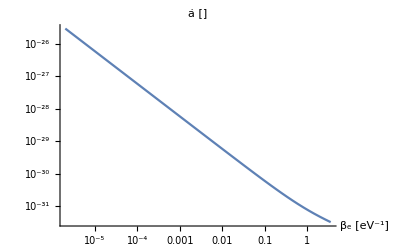

```mathematica
LogLogPlot[aH[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"ȧ []",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
```

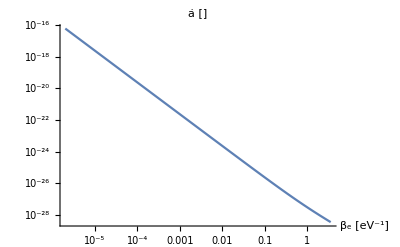

```mathematica
LogLogPlot[H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"ȧ []",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
```

#### Screening length comparison and Expected rate scaling

Λ and 1/(Z_1 β ȧ) control the scaling of the rate

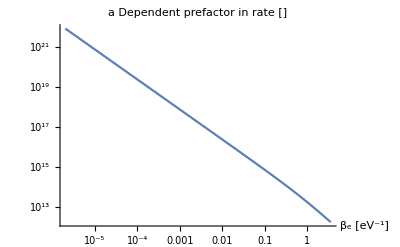

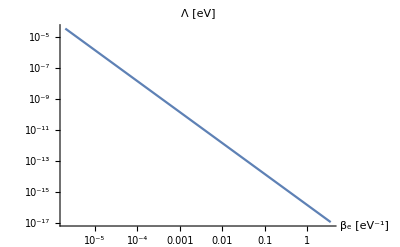

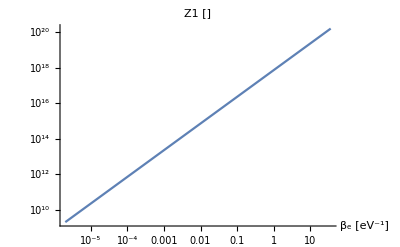

```mathematica
LogLogPlot[1/(Z1[β] aH[β]β)/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"a Dependent prefactor in rate []",AxesLabel->{"β_e [eV^-1]"}]
LogLogPlot[Λ[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV^-1]"}]
LogLogPlot[Z1[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],10/("TR")/.CosmoParams[]},PlotLabel->"Z1 []",AxesLabel->{"β_e [eV^-1]"}]
```

So it seems like partition function dominates over temperature scaling of a, and the reduced screening at late times.

```mathematica
Z1[1/("Td")]/.CosmoParams[]
```

2.00913×10^9

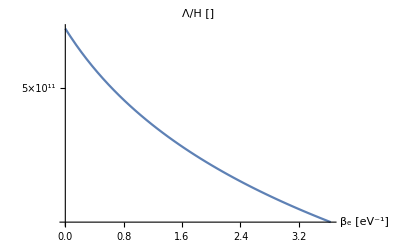

```mathematica
LogPlot[Λ[β]/H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"Λ/H []",AxesLabel->{"β_e [eV^-1]"}]
```

Screening length (Debeye momentum) - minimum momentum transfered

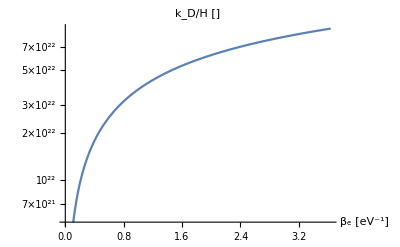

```mathematica
LogPlot[(√(2 "me" Λ[β]))/H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"k_D/H []",AxesLabel->{"β_e [eV^-1]"}]
```

#### Rate and Energy plots - SM aDM mass values

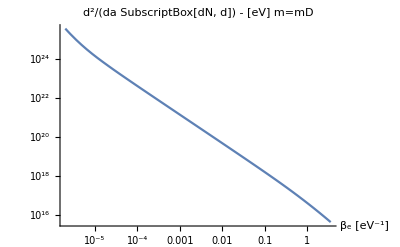

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

m=mD

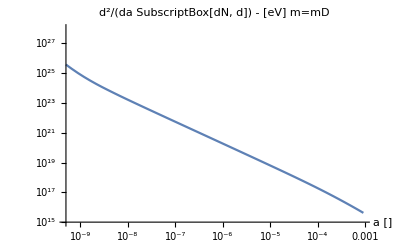

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

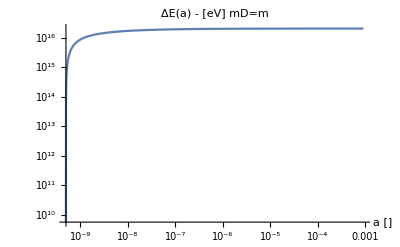

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=m",AxesLabel->{"a []"},PlotRange->All]
```

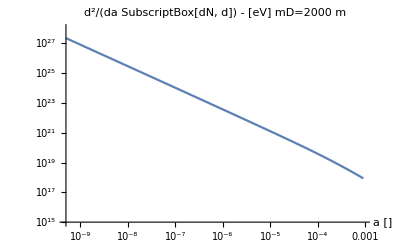

```mathematica
LogLogPlot[10^inter2000me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] mD=2000 m",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

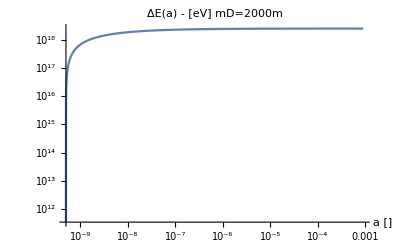

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=2000m",AxesLabel->{"a []"},PlotRange->All]
```

#### Neff constraint

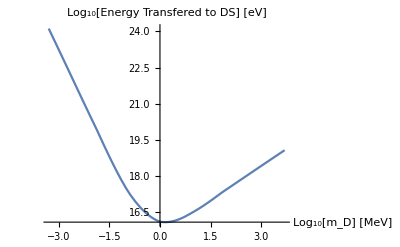

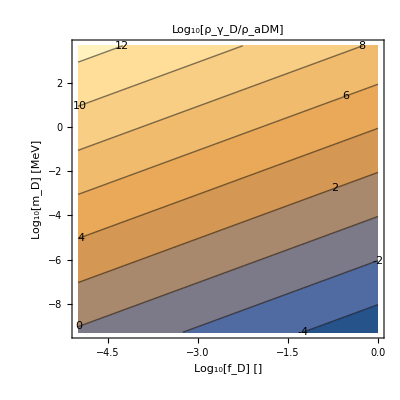

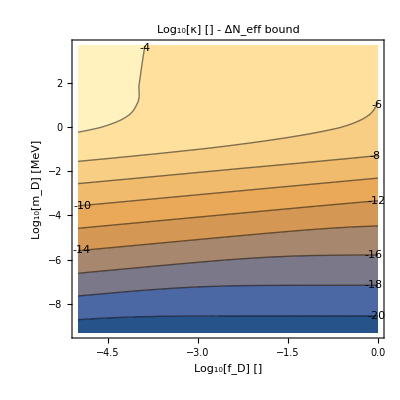

```mathematica
ComputeΔNeffConstraint[testΔEdict]
```